```mathematica
NS[]
```

```mathematica
updatepar[given_,k0_,mu0_,nu0_,s0_]:=Block[{k,mu,s,nu,ngiven=Length@T@given,mugiven,ncovgiven},
If[ngiven>0,

mugiven=Mean/@given;
ncovgiven=(given-Mean@T@given).T[given-Mean@T@given];
k=k0+ngiven;

{k,(k0*mu0+ngiven*mugiven)/k,nu0+ngiven,s0+ncovgiven+k0*ngiven*(T[{mugiven-mu0}].{mugiven-mu0})/k},

{k0,mu0,nu0,s0}]
];
```

```mathematica
predpost[want_,given_,k0_,mu0_,nu0_,s0_]:=Block[{d=Length@want,k,mu,srow,scol,nu,nwant=Length[T@want]},

{k,mu,nu,srow}=updatepar[given,k0,mu0,nu0,s0];

scol=IdentityMatrix[nwant]+Table[1,nwant,nwant]/k;

PDF[MatrixTDistribution[T[Table[mu,nwant]],srow,scol,nu-d+1],want]
];
```

```mathematica
logpredpost[want_,given_,k0_,mu0_,nu0_,s0_]:=Block[{d=Length@want,k,mu,srow,scol,nu,nwant=Length[T@want]},

{k,mu,nu,srow}=updatepar[given,k0,mu0,nu0,s0];

scol=IdentityMatrix[nwant]+Table[1,nwant,nwant]/k;

LogLikelihood[MatrixTDistribution[T[Table[mu,nwant]],srow,scol,nu-d+1],{want}]
];
```

```mathematica
testwant=RandomReal[{-5,5},{4,1}];
testgiven=RandomReal[{-5,5},{4,1}];
testk0=5;testmu0=RandomReal[{-5,5},4];
testnu0=20;
tests0=Block[{l=UpperTriangularize[RandomReal[{-5,5},{4,4}]]},T[l].l];
```

```mathematica
MF/@updatepar[testgiven,testk0,testmu0,testnu0,tests0]
```

{6,(3.19311
2.62305
-3.72437
-1.29712),21,(72.859 | -3.00269 | -39.549 | 38.6584
-3.00269 | 21.6595 | -0.851041 | -6.15765
-39.549 | -0.851041 | 26.6012 | -12.737
38.6584 | -6.15765 | -12.737 | 54.8846)}

```mathematica
predpost[testwant,testgiven,testk0,testmu0,testnu0,tests0]
```

1.62964×10^-16

```mathematica
logpredpost[testwant,testgiven,testk0,testmu0,testnu0,tests0]
```

-36.353

```mathematica
(* test formula *)
```

```mathematica
prob=predpost[testwant[[;;,{1}]],testgiven,testk0,testmu0,testnu0,tests0];

Do[
prob=prob*predpost[testwant[[;;,{i}]],T[Join[T@testgiven,T[testwant[[;;,;;(i-1)]]]]],testk0,testmu0,testnu0,tests0],
{i,2,Length[T@testwant]}]
```

```mathematica
prob
```

1.62964×10^-16

```mathematica
1-(prob/predpost[testwant,testgiven,testk0,testmu0,testnu0,tests0])
```

0.

```mathematica
prob2=predpost[T@Join[T@testwant,T@testgiven],Table[{},Length@testwant],testk0,testmu0,testnu0,tests0]/predpost[testgiven,Table[{},Length@testwant],testk0,testmu0,testnu0,tests0]
```

1.62964×10^-16

```mathematica
1-(prob2/predpost[testwant,testgiven,testk0,testmu0,testnu0,tests0])
```

6.99441×10^-15

```mathematica
(* apply to fMRI data *)
```

```mathematica
sdata=Import["..\\nanunana_fmri\\latest_code\\weights_Schizo_40cons"];Dimensions[sdata]
```

{40,49}

```mathematica
hdata=Import["..\\nanunana_fmri\\latest_code\\weights_con_40cons"];Dimensions[hdata]
```

{40,55}

```mathematica
ns=Length@T@sdata;nh=Length@T@hdata;
```

```mathematica
ClearAll[tan,dtan];tan[x_]=Tan[Pi*x/2];SetAttributes[tan,Listable];
dtan[x_]=Pi/(1+Cos[Pi*x]);SetAttributes[dtan,Listable];
```

```mathematica
ClearAll[tlogpredpost,tclogpredpost];tclogpredpost[want_,given_]:=Block[{d=Length@want},logpredpost[tan[want],tan[given],1,Table[0,d],d+1,(d+2)*IdentityMatrix[d]/4]+Total@Log@Flatten[dtan[want]]];

tlogpredpost[want_]:=Block[{d=Length@want},logpredpost[tan[want],Table[{},d],1,Table[0,d],d+1,(d+2)*IdentityMatrix[d]/4]+Total@Log@Flatten[dtan[want]]];
```

```mathematica
ClearAll[nlogpredpost,nclogpredpost];nclogpredpost[want_,given_]:=Block[{d=Length@want},logpredpost[want,given,1,Table[0,d],d+1,10*IdentityMatrix[d]]];

nlogpredpost[want_]:=Block[{d=Length@want},logpredpost[want,Table[{},d],1,Table[0,d],d+1,10*IdentityMatrix[d]]];
```

```mathematica
MF[{tlogpredpost@#,nlogpredpost@#}&/@{sdata,hdata}]
```

(-980.982 | -1224.44
-877.26 | -1263.7)

```mathematica
Total@%
```

{-1858.24,-2488.14}

```mathematica
rg=Range[nd];MF[{{Mean@Table[tclogpredpost[sdata[[;;,{i}]],sdata[[;;,Delete[Range[Length@T@sdata],i]]]],{i,Length@T@sdata}],
Mean@Table[nclogpredpost[sdata[[;;,{i}]],sdata[[;;,Delete[Range[Length@T@sdata],i]]]],{i,Length@T@sdata}]},

{Mean@Table[tclogpredpost[hdata[[;;,{i}]],hdata[[;;,Delete[Range[Length@T@hdata],i]]]],{i,Length@T@hdata}],
Mean@Table[nclogpredpost[hdata[[;;,{i}]],hdata[[;;,Delete[Range[Length@T@hdata],i]]]],{i,Length@T@hdata}]}}]
```

(-19.8438 | -18.2458
-14.4001 | -15.9095)

```mathematica
Total[%]
```

{-34.2439,-34.1553}

```mathematica
(* Check which components of the data lead to discrepancy between evidence and log-score *)
MF@Table[
cdata=hdata[[{k}]];nd=Length@T@cdata;rg=Range[nd];
{k,(tlogpredpost@#-nlogpredpost@#)&@cdata,

Mean@Table[tclogpredpost[cdata[[;;,{i}]],cdata[[;;,Delete[rg,i]]]],{i,nd}]-
Mean@Table[nclogpredpost[cdata[[;;,{i}]],cdata[[;;,Delete[rg,i]]]],{i,nd}]},
{k,Length@hdata}]
```

(1 | 17.2186 | 0.0463278
2 | 16.4688 | 0.0638563
3 | 8.45339 | -0.115485
4 | 19.2301 | 0.0989031
5 | 15.7169 | 0.0175952
6 | 20.9862 | 0.140154
7 | 24.5395 | 0.196163
8 | 20.1912 | 0.127076
9 | 23.4577 | 0.177603
10 | 12.4483 | -0.0527461
11 | 24.0537 | 0.149573
12 | 10.2918 | -0.129024
13 | 24.4395 | 0.164336
14 | 18.4974 | 0.0251245
15 | 22.3692 | 0.160359
16 | 57.9664 | 0.751407
17 | -12.4063 | -0.504123
18 | 22.4867 | 0.183029
19 | 13.1225 | -0.00116054
20 | 22.5119 | 0.181447
21 | 24.8889 | 0.208111
22 | 12.0447 | -0.0529893
23 | 7.64634 | -0.226408
24 | 4.67466 | -0.195043
25 | 21.4011 | 0.153436
26 | 21.488 | 0.15782
27 | 5.30931 | -0.216425
28 | 21.9059 | 0.0463138
29 | 13.1114 | -0.0296165
30 | 0.368831 | -0.439913
31 | 22.0737 | 0.161818
32 | 22.0366 | 0.153827
33 | 19.5114 | 0.0458418
34 | 21.0458 | 0.124044
35 | 21.49 | 0.0468544
36 | 9.6643 | -0.142263
37 | 9.69455 | -0.125646
38 | 19.7262 | 0.107236
39 | 22.0534 | 0.164326
40 | 12.4848 | -0.0547997)

```mathematica
cdata=hdata[[{12,23}]];nd=Length@T@cdata;rg=Range[nd];
```

```mathematica
{tlogpredpost@#,nlogpredpost@#}&@cdata
```

{-68.0015,-87.4624}

```mathematica
Differences[%]
```

{-19.4609}

```mathematica
{tlogsc=Mean@Table[tclogpredpost[cdata[[;;,{i}]],cdata[[;;,Delete[rg,i]]]],{i,nd}],
nlogsc=Mean@Table[nclogpredpost[cdata[[;;,{i}]],cdata[[;;,Delete[rg,i]]]],{i,nd}]}
```

{-1.39229,-1.02383}

```mathematica
Differences[%]
```

{0.368457}

```mathematica
tseqev=Table[tlogpredpost[cdata[[;;,;;i]]],{i,2,nd}];
nseqev=Table[nlogpredpost[cdata[[;;,;;i]]],{i,2,nd}];
```

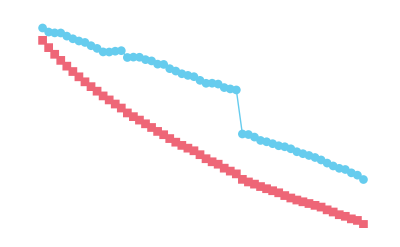

```mathematica
ListPlot[{tseqev,nseqev},Joined->True,PlotMarkers->Auto,PlotRange->{All,All}]
```

```mathematica
tseqpred=Table[tclogpredpost[cdata[[;;,{i}]],cdata[[;;,;;(i-1)]]],{i,2,nd}];nseqpred=Table[nclogpredpost[cdata[[;;,{i}]],cdata[[;;,;;(i-1)]]],{i,2,nd}];
```

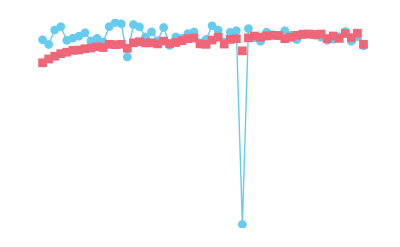

```mathematica
ListPlot[{tseqpred,nseqpred},Joined->True,PlotMarkers->Auto,PlotRange->{All,All}]
```

```mathematica
nshuffle=100;
```

```mathematica
SeedRandom[999];
tmeanseqev=Mean@Table[ord=RandomSample[Range[nd]];
Table[tlogpredpost[cdata[[;;,ord[[;;i]]]]],{i,2,nd}]
,nshuffle];
```

```mathematica
SeedRandom[999];
nmeanseqev=Mean@Table[ord=RandomSample[Range[nd]];
Table[nlogpredpost[cdata[[;;,ord[[;;i]]]]],{i,2,nd}]
,nshuffle];
```

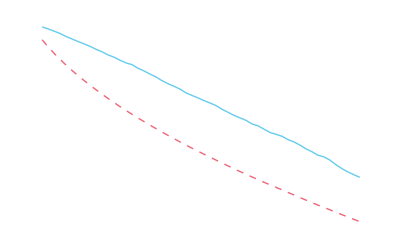
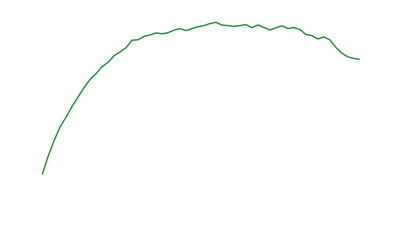

```mathematica
{ListPlot[{tmeanseqev,nmeanseqev},Joined->True,PlotMarkers->None,PlotRange->{All,All},ImageSize->a4shortside/1.5],ListPlot[tmeanseqev-nmeanseqev,Joined->True,PlotMarkers->None,PlotStyle->green,PlotRange->{All,All},ImageSize->a4shortside/1.5]}
```

```mathematica
{tlogpredpost@#,nlogpredpost@#}&@cdata
```

{-68.0015,-87.4624}

```mathematica
nshuffle=500;
```

```mathematica
SeedRandom[999];
tmeanseqpred=Mean@Table[ord=RandomSample[Range[nd]];
Table[tclogpredpost[cdata[[;;,{ord[[i]]}]],cdata[[;;,ord[[;;(i-1)]]]]],{i,2,nd}]
,nshuffle];
```

```mathematica
SeedRandom[999];
nmeanseqpred=Mean@Table[ord=RandomSample[Range[nd]];
Table[nclogpredpost[cdata[[;;,{ord[[i]]}]],cdata[[;;,ord[[;;(i-1)]]]]],{i,2,nd}]
,nshuffle];
```

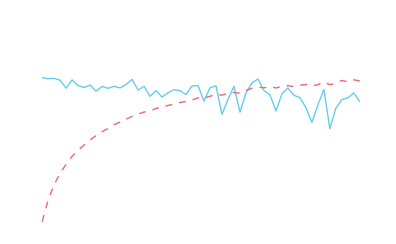
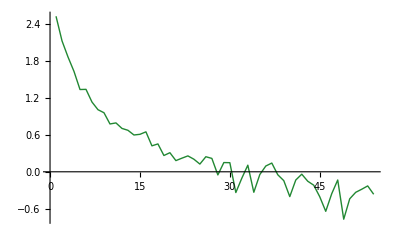

```mathematica
{ListPlot[{tmeanseqpred,nmeanseqpred},Joined->True,PlotMarkers->None,PlotRange->{All,All},ImageSize->a4shortside/1.5],
ListPlot[tmeanseqpred-nmeanseqpred,Joined->True,PlotMarkers->None,Axes->{True,False},PlotStyle->green,PlotRange->{All,All},ImageSize->a4shortside/1.5]}
```

```mathematica
{Mean@Table[tclogpredpost[cdata[[;;,{i}]],cdata[[;;,Delete[rg,i]]]],{i,nd}],
Mean@Table[nclogpredpost[cdata[[;;,{i}]],cdata[[;;,Delete[rg,i]]]],{i,nd}]}
```

{-1.39229,-1.02383}

```mathematica
(* Check which components of the data lead to discrepancy between evidence and log-score *)
MF@Table[
cdata=sdata[[{k}]];nd=Length@T@cdata;rg=Range[nd];
{k,(tlogpredpost@#-nlogpredpost@#)&@cdata,

Mean@Table[tclogpredpost[cdata[[;;,{i}]],cdata[[;;,Delete[rg,i]]]],{i,nd}]-
Mean@Table[nclogpredpost[cdata[[;;,{i}]],cdata[[;;,Delete[rg,i]]]],{i,nd}]},
{k,Length@hdata}]
```

(1 | 13.8686 | -0.044937
2 | 18.1706 | 0.131994
3 | 19.6707 | 0.173272
4 | -51.9717 | -2.526
5 | 22.8983 | 0.202613
6 | 23.8713 | 0.22701
7 | 19.995 | 0.163372
8 | -14.8348 | -0.945361
9 | 13.042 | 0.000997891
10 | 19.605 | 0.172356
11 | 16.7408 | 0.0502144
12 | 17.6316 | 0.143352
13 | 14.1326 | 0.0638239
14 | 10.7949 | -0.141099
15 | -1.31122 | -0.294741
16 | 17.0779 | 0.114661
17 | 19.1619 | 0.178371
18 | 21.1205 | 0.182736
19 | 9.37748 | -0.0984317
20 | -73.1529 | -3.24316
21 | -66.6788 | -2.669
22 | 10.1235 | -0.108329
23 | 7.75674 | -0.14443
24 | 23.747 | 0.226104
25 | -6.87954 | -0.448856
26 | -69.5064 | -3.05982
27 | 24.1214 | 0.213228
28 | 11.3655 | -0.0302781
29 | 11.6457 | -0.0203288
30 | -13.9212 | -0.918875
31 | -40.469 | -1.6408
32 | -76.0883 | -3.0058
33 | 13.0539 | -0.0320591
34 | -56.7355 | -2.31038
35 | 21.0526 | 0.150756
36 | 16.4182 | 0.112116
37 | 10.7346 | -0.0135945
38 | -76.4879 | -3.01094
39 | -10.8373 | -0.749946
40 | 4.29374 | -0.232552)

```mathematica
cdata=sdata[[{14,40}]];nd=Length@T@cdata;rg=Range[nd];
```

```mathematica
{tlogpredpost@#,nlogpredpost@#}&@cdata
```

{-62.9103,-85.5609}

```mathematica
Differences[%]
```

{-22.6506}

```mathematica
{tlogsc=Mean@Table[tclogpredpost[cdata[[;;,{i}]],cdata[[;;,Delete[rg,i]]]],{i,nd}],
nlogsc=Mean@Table[nclogpredpost[cdata[[;;,{i}]],cdata[[;;,Delete[rg,i]]]],{i,nd}]}
```

{-1.37954,-1.20594}

```mathematica
Differences[%]
```

{0.1736}

```mathematica
tseqev=Table[tlogpredpost[cdata[[;;,;;i]]],{i,2,nd}];
nseqev=Table[nlogpredpost[cdata[[;;,;;i]]],{i,2,nd}];
```

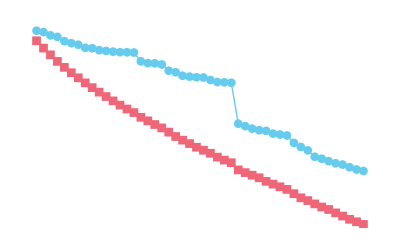

```mathematica
ListPlot[{tseqev,nseqev},Joined->True,PlotMarkers->Auto,PlotRange->{All,All}]
```

```mathematica
tseqpred=Table[tclogpredpost[cdata[[;;,{i}]],cdata[[;;,;;(i-1)]]],{i,2,nd}];nseqpred=Table[nclogpredpost[cdata[[;;,{i}]],cdata[[;;,;;(i-1)]]],{i,2,nd}];
```

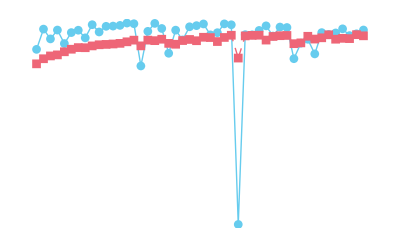

```mathematica
ListPlot[{tseqpred,nseqpred},Joined->True,PlotMarkers->Auto,PlotRange->{All,All}]
```

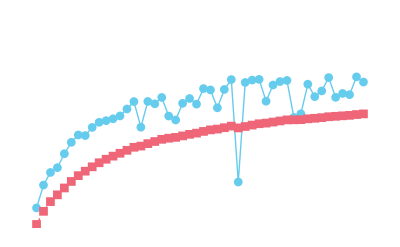

```mathematica
ListPlot[{nseqpred,nseqev/Range[2,nd]},Joined->True,PlotMarkers->Auto,PlotRange->{All,All}]
```

```mathematica
nshuffle=100;
```

```mathematica
SeedRandom[999];
tmeanseqev=Mean@Table[ord=RandomSample[Range[nd]];
Table[tlogpredpost[cdata[[;;,ord[[;;i]]]]],{i,2,nd}]
,nshuffle];
```

```mathematica
SeedRandom[999];
nmeanseqev=Mean@Table[ord=RandomSample[Range[nd]];
Table[nlogpredpost[cdata[[;;,ord[[;;i]]]]],{i,2,nd}]
,nshuffle];
```

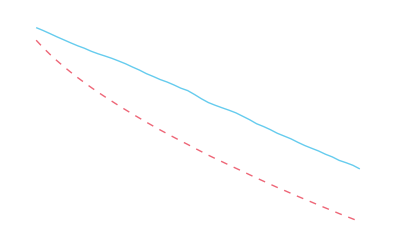
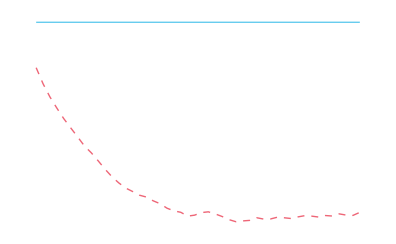
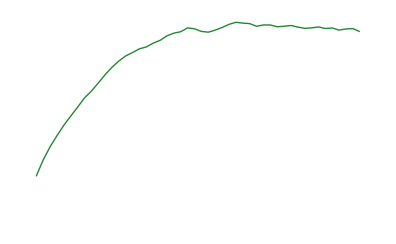

```mathematica
{ListPlot[{tmeanseqev,nmeanseqev},Joined->True,PlotMarkers->None,PlotRange->{All,All},ImageSize->a4shortside/1.5,FrameLabel->{"data size",Row[{ln," ", "p","(data|model)"}]},FrameStyle->Directive[FontSize->15]],

norm=Log[Exp@tmeanseqev+Exp@nmeanseqev];
ListPlot[{tmeanseqev-norm,nmeanseqev-norm},Joined->True,PlotMarkers->None,PlotRange->{All,All},ImageSize->a4shortside/1.5,FrameLabel->{"data size",Row[{ln," ", "p","(model|data)"}]},FrameStyle->Directive[FontSize->15]],ListPlot[tmeanseqev-nmeanseqev,Joined->True,PlotMarkers->None,PlotStyle->green,PlotRange->{All,All},ImageSize->a4shortside/1.5,FrameLabel->{"data size","difference"},FrameStyle->Directive[FontSize->15]]}
```

```mathematica
{tlogpredpost@#,nlogpredpost@#}&@cdata
```

{-62.9103,-85.5609}

```mathematica
nshuffle=500;
```

```mathematica
SeedRandom[999];
tmeanseqpred=Mean@Table[ord=RandomSample[Range[nd]];
Table[tclogpredpost[cdata[[;;,{ord[[i]]}]],cdata[[;;,ord[[;;(i-1)]]]]],{i,2,nd}]
,nshuffle];
```

```mathematica
SeedRandom[999];
nmeanseqpred=Mean@Table[ord=RandomSample[Range[nd]];
Table[nclogpredpost[cdata[[;;,{ord[[i]]}]],cdata[[;;,ord[[;;(i-1)]]]]],{i,2,nd}]
,nshuffle];
```

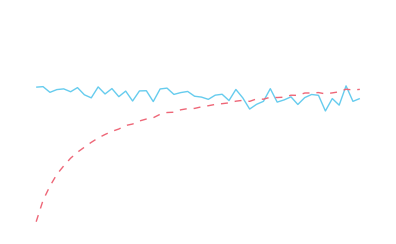
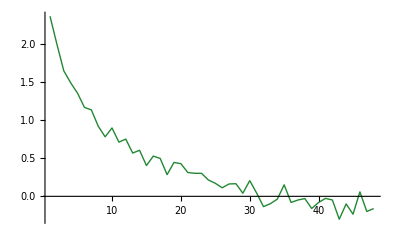

```mathematica
{ListPlot[{tmeanseqpred,nmeanseqpred},Joined->True,PlotMarkers->None,PlotRange->{All,All},ImageSize->a4shortside/1.5,FrameLabel->{"data size","leave-one-out"},FrameStyle->Directive[FontSize->15]],
ListPlot[tmeanseqpred-nmeanseqpred,Joined->True,PlotMarkers->None,Axes->{True,False},PlotStyle->green,PlotRange->{All,All},ImageSize->a4shortside/1.5,FrameLabel->{"data size","difference"},FrameStyle->Directive[FontSize->15]]}
```

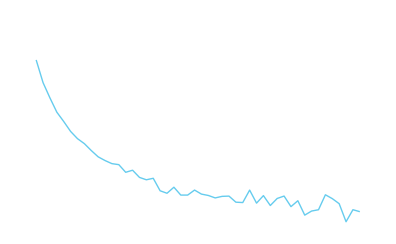

```mathematica
ListPlot[{1-nmeanseqev/Range[2,nd]/nmeanseqpred},Joined->True,PlotMarkers->None,PlotRange->{All,All},ImageSize->a4shortside/1.5,FrameLabel->{"data size",""},FrameStyle->Directive[FontSize->15]]
```

```mathematica
{Mean@Table[tclogpredpost[cdata[[;;,{i}]],cdata[[;;,Delete[rg,i]]]],{i,nd}],
Mean@Table[nclogpredpost[cdata[[;;,{i}]],cdata[[;;,Delete[rg,i]]]],{i,nd}]}
```

{-1.39229,-1.02383}

```mathematica
testdata2=T@Join[T@(hdata[[{1}]]),T@(sdata[[{1}]])];
```

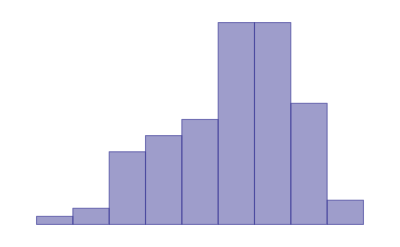

```mathematica
Histogram[testdata2,"Knuth",PDF,PlotRange->{All,All},ImageSize->a4shortside/2]
```

```mathematica
cdata=testdata2;nd=Length@T@cdata
```

104

```mathematica
nshuffle=200;
```

```mathematica
SeedRandom[999];
tmeanseqpred=Mean@ParallelTable[ord=RandomSample[Range[nd]];
Table[tclogpredpost[cdata[[;;,{ord[[i]]}]],cdata[[;;,ord[[;;(i-1)]]]]],{i,2,nd}]
,nshuffle,Method->"CoarsestGrained"];
```

```mathematica
SeedRandom[999];
nmeanseqpred=Mean@ParallelTable[ord=RandomSample[Range[nd]];
Table[nclogpredpost[cdata[[;;,{ord[[i]]}]],cdata[[;;,ord[[;;(i-1)]]]]],{i,2,nd}]
,nshuffle,Method->"CoarsestGrained"];
```

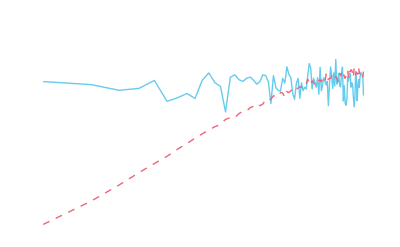

```mathematica
ListLogLinearPlot[{tmeanseqpred,nmeanseqpred},Joined->True,PlotMarkers->None,PlotRange->{All,{All,All}}]
```

```mathematica
{tlogpredpost[cdata],nlogpredpost[cdata]}
```

{-57.9544,-68.4969}

```mathematica
nshuffle=5;
```

```mathematica
SeedRandom[999];
tmeanseqev=Mean@ParallelTable[ord=RandomSample[Range[nd]];
Table[tlogpredpost[cdata[[;;,ord[[;;i]]]]],{i,2,nd}]
,nshuffle,Method->"CoarsestGrained"];
```

```mathematica
SeedRandom[999];
nmeanseqev=Mean@ParallelTable[ord=RandomSample[Range[nd]];
Table[nlogpredpost[cdata[[;;,ord[[;;i]]]]],{i,2,nd}]
,nshuffle,Method->"CoarsestGrained"];
```

```mathematica
norm=Log[Exp@tmeanseqev+Exp@nmeanseqev];
```

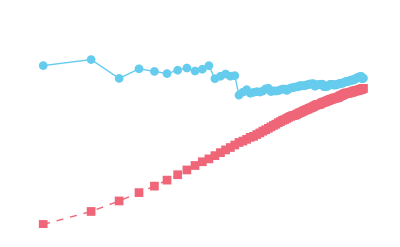

```mathematica
ListLogLinearPlot[{tmeanseqev/Range[2,nd],nmeanseqev/Range[2,nd]},Joined->True,PlotMarkers->Auto,PlotRange->{All,All}]
```

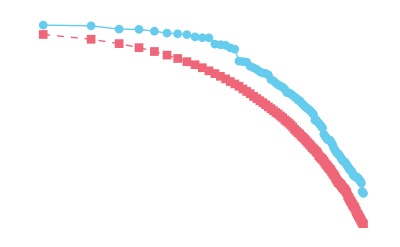

```mathematica
ListLogLinearPlot[{tmeanseqev,nmeanseqev},Joined->True,PlotMarkers->Auto,PlotRange->{All,All}]
```

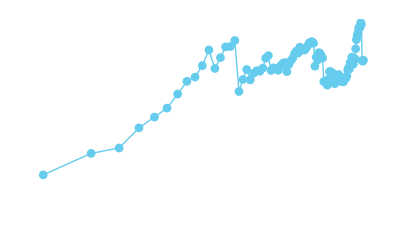

```mathematica
ListLogLinearPlot[tmeanseqev-nmeanseqev,Joined->True,PlotMarkers->Auto,PlotRange->{All,All}]
```

```mathematica
SeedRandom[999];testdata={RandomVariate[TruncatedDistribution[{-1,1},NormalDistribution[0,1/2]],1000]};
```

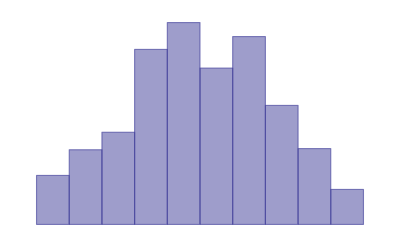

```mathematica
Histogram[testdata,"Knuth",PDF,PlotRange->{All,All},ImageSize->a4shortside/2]
```

```mathematica
cdata=testdata;nd=Length@T@cdata;
```

```mathematica
nshuffle=10;
```

```mathematica
SeedRandom[999];
tmeanseqpred=Mean@ParallelTable[ord=RandomSample[Range[nd]];
Table[tclogpredpost[cdata[[;;,{ord[[i]]}]],cdata[[;;,ord[[;;(i-1)]]]]],{i,2,nd}]
,nshuffle,Method->"CoarsestGrained"];
```

```mathematica
SeedRandom[999];
nmeanseqpred=Mean@ParallelTable[ord=RandomSample[Range[nd]];
Table[nclogpredpost[cdata[[;;,{ord[[i]]}]],cdata[[;;,ord[[;;(i-1)]]]]],{i,2,nd}]
,nshuffle,Method->"CoarsestGrained"];
```

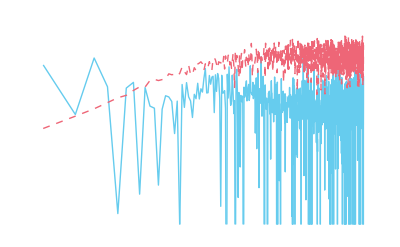

```mathematica
ListLogLinearPlot[{tmeanseqpred,nmeanseqpred},Joined->True,PlotMarkers->None,PlotRange->{All,{Auto,All}}]
```

```mathematica
nshuffle=2;
```

```mathematica
SeedRandom[999];
tmeanseqev=Mean@ParallelTable[ord=RandomSample[Range[nd]];
Table[tlogpredpost[cdata[[;;,ord[[;;i]]]]],{i,2,200}]
,nshuffle,Method->"CoarsestGrained"];
```

```mathematica
SeedRandom[999];
nmeanseqev=Mean@ParallelTable[ord=RandomSample[Range[nd]];
Table[nlogpredpost[cdata[[;;,ord[[;;i]]]]],{i,2,200}]
,nshuffle,Method->"CoarsestGrained"];
```

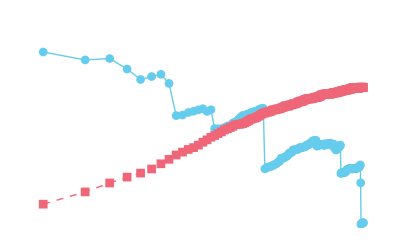

```mathematica
ListLogLinearPlot[{tmeanseqev/Range[2,200],nmeanseqev/Range[2,200]},Joined->True,PlotMarkers->Auto,PlotRange->{All,All}]
```